```mathematica
(*Initialisation - Run first*)
SetEnvironment["OMP_NUM_THREADS"->"8"]
(*Replace the following with the appropriate pathways for your device*)
Import["/Users/questuser/Documents/QuESTlink/Link/QuESTlink.m"] (*QuESTlink load*)
CreateLocalQuESTEnv["/Users/questuser/Documents/Kathryn/quest_link"]; (*Creating QuEST environment*)
Import["/Users/questuser/Documents/Kathryn/Rydberg Custom Gates Custom SWAP.wl"]; (*Configuration File*)
data=Import["/Users/questuser/Documents/Kathryn/SU4Gates9Qubits.csv"]; (*Imported gates from Qiskit*)
(*Import["C:\\Users\\KitKa\\QuESTlink\\Link\\QuESTlink.m"] (*QuESTlink load*)
CreateLocalQuESTEnv["C:\\Users\\KitKa\\QuESTlink\\quest_link.exe"];(*Creating QuEST environment*)Import["C:\\Users\\KitKa\\QuESTlink\\Rydberg Custom Gates Custom SWAP.wl"];(*Configuration File*)data=Import["C:\\Users\\KitKa\\OneDrive\\Documents\\Wolfram Mathematica\\SU4Gates9Qubits.csv"];*)
userconfig=<|
NQubits-> 9,
QubitLocations->Association[#1->#2&@@@Transpose@{Range[0,8],{{0,0,0},{0,1,0},{1,0,0},{1,1,0},{0,2,0},{1,2,0},{2,0,0},{2,1,0},{2,2,0}}}],
(* blockade radius in μm*)
BlockadeRadius->10,
(* inter-atomic separation in μm. This will be the unit of the lattice given in qubitLocations *)
UnitLattice->1,
(* T1=τvac/nqubits in μs *)
VacuumLifeTime->4*10^6,
(* the γ noise on theq initialization *)
LeakProbInit->0.007,
(* duration on the initialization *)
DurInit->300,
(* measurement induces atom loss afterward *)
FidMeas-> 100,
DurMeas-> 2*10^4,
(* the increasing chance of atom loss due to measurement, in percent *)
AtomLossMeas-> 0,
(* mostly used in the single qubit noise, unit μs. It's presumed that Subscript[T, 2]^* has been echoed out to Subscript[T, 2] *)
T2->1.49*10^6,
(* leak probability of implementing multi-qubit gates *)
LeakProbCZ-> <|01-> 0.001,11->0.001 |>,
(* Rabi frequency, MHz *)
Ω->1,
(* fidelity of swap operation *)
FidSWAP->99.7
|>;
RydDev=CreateRydbergDevice[userconfig];
RydDev[InitLocations]
(*Defining QuEST's Rydberg Blockade Check in a permanent function such that it can be used without constantly editing the code*)
qubitLocs=userconfig[QubitLocations];
distloc[q1_,q2_]:=Norm[qubitLocs[q1]-qubitLocs[q2],2]*userconfig[UnitLattice];
blockadeCheck[q_List]:=And@@((distloc@@#<= userconfig[BlockadeRadius])&/@Subsets[Flatten[q],{2}]);
```

-Graphics3D-

```mathematica
Fraction[a_,b_]:=a/b
KetList[NQ_]:=Table[ToExpression@StringSplit[IntegerString[i,2,NQ],""],{i,0,2^NQ-1,1}]
(*Fully Translate Qiskit output into QuEST format, SWAP Procedure*)

MeasErrors[QubitList_]:=Table[Subscript[U,QubitList[[i]]][{{0.9997,0},{0,1.0003}}],{i,1,Length[QubitList]}]
```

```mathematica
KetList[3]
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

U_(0,1,2)[{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0}}]

-Graphics-

U_(0,1,2)[{{1,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,0,0,-1,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,-1}}]

{X_0,X_1,X_2,H_0,X_0,U_(0,1,2)[{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0}}],X_0,H_0,X_0,X_1,X_2}

{X_0,X_1,X_2,H_0,X_0,U_(0,1,2)[{{1,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,0,0,-1,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,-1}}],X_0,H_0,X_0,X_1,X_2}

{H_0,U_(0,1,2)[{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0}}],H_0}

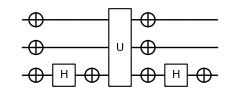

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)

-Graphics-

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

```mathematica
Toff=Subscript[U, 0,1,2][{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0}}]
DrawCircuit[{Toff}]
CCZ=Subscript[U, 0,1,2][{{1,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,0,0,-1,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,-1}}]
CCZCirc={Subscript[X, 0],Subscript[X, 1],Subscript[X, 2],Subscript[H, 0],Subscript[X, 0],Toff,Subscript[X, 0],Subscript[H, 0],Subscript[X, 0],Subscript[X, 1],Subscript[X, 2]}
ToffCirc={Subscript[X, 0],Subscript[X, 1],Subscript[X, 2],Subscript[H, 0],Subscript[X, 0],CCZ,Subscript[X, 0],Subscript[H, 0],Subscript[X, 0],Subscript[X, 1],Subscript[X, 2]}
CCZClifCirc={Subscript[H, 0],Toff,Subscript[H, 0]}(*{Subscript[X,1],Subscript[X,2],Subscript[X, 0],CCZ,Subscript[X, 0],Subscript[X,1],Subscript[X,2]}*)
DrawCircuit[ToffCirc]
CalcCircuitMatrix[{Toff}]//MatrixForm
CalcCircuitMatrix[ToffCirc]//MatrixForm
DrawCircuit[CCZCirc]
CalcCircuitMatrix[{CCZ}] //MatrixForm
CalcCircuitMatrix[CCZCirc] // MatrixForm
CalcCircuitMatrix[CCZClifCirc]//MatrixForm
```

```mathematica
{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0}}//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

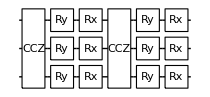
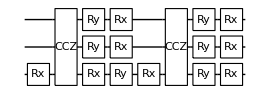
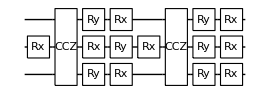
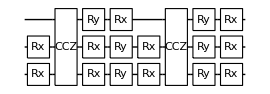
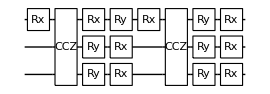
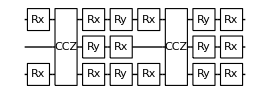
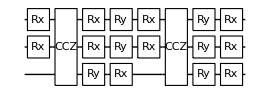
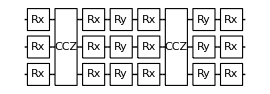

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

{{0.933367,0.00773659,0.00773659,0.00771312,0.00773659,0.00771312,0.00771312,0.00776832},{0.00773795,0.933358,0.00771387,0.00773902,0.00771387,0.00773902,0.00776899,0.00771382},{0.00773795,0.00771387,0.933358,0.00773902,0.00771387,0.00776899,0.00773902,0.00771382},{0.00771367,0.00773771,0.00773771,0.93336,0.0077688,0.00771362,0.00771362,0.00773877},{0.00773795,0.00771387,0.00771387,0.00776899,0.933358,0.00773902,0.00773902,0.00771382},{0.00771367,0.00773771,0.0077688,0.00771362,0.00773771,0.93336,0.00771362,0.00773877},{0.00771367,0.0077688,0.00773771,0.00771362,0.00773771,0.00771362,0.93336,0.00773877},{0.0077685,0.00771333,0.00771333,0.00773682,0.00771333,0.00773682,0.00773682,0.933365}}

```mathematica
InitCirc[NQ_]:=Table[Subscript[Init, b],{b,0,NQ-1,1}]
GroverIteration3Q[SearchSeed_]:=Module[{XIndices=Position[Reverse[SearchSeed],1]},
Xs=Table[XTrans[XIndices[[j,1]]-1],{j,1,Length[XIndices]}];
Flatten[{Xs,Subscript[CCZ, 0,1,2],Xs,HTrans[0],HTrans[1],HTrans[2],Subscript[CCZ, 0,1,2],HTrans[0],HTrans[1],HTrans[2]}]]
Table[DrawCircuit[GroverIteration3Q[KetList[3][[i]]]],{i,1,8}]
KetList[3]
GroversAlg3Q=Table[SearchSeeds=KetList[3];
ρ=CreateDensityQureg[9];
(*InitZeroState[ρ];*)
InitialisationCirc=ExtractCircuit[GetCircuitSchedule[Join[InitCirc[3],HTrans[0],HTrans[1],HTrans[2]],RydDev,ReplaceAliases->True]];
ApplyCircuit[ρ,InitialisationCirc];
Gr=ExtractCircuit[InsertCircuitNoise[GroverIteration3Q[SearchSeeds[[i]]],RydDev,ReplaceAliases->True]];
ApplyCircuit[ρ,Join[Gr,Gr]];CalcProbOfAllOutcomes[ρ,{0,1,2}],{i,1,8}]

DestroyAllQuregs[];
```

```mathematica
XTrans[i_]:={Subscript[Rx, i][Pi]};
HTrans[i_]:={Subscript[Ry, i][Pi/2],Subscript[Rx, i][Pi]};
ToffSandBread[t_,c1_,c2_]:={Subscript[Ry, t][-Pi/2],Subscript[Rx, t][-Pi],Subscript[Rx, c1][Pi],Subscript[Rx, c2][Pi]}
```

```mathematica
Toff[t_,c1_,c2_]:=Subscript[U, t,c1,c2][{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0}}]
CCZGate[t_,c1_,c2_]:=Subscript[U, t,c1,c2][{{1,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,0,0,-1,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,-1}}]
```

```mathematica
ToffRyd[t_,c1_,c2_]:={{Subscript[X, t],Subscript[X, c1],Subscript[X, c2],Subscript[H, t],Subscript[X, t],CCZGate[t,c1,c2],Subscript[X, t],Subscript[H, t],Subscript[X, t],Subscript[X, c1],Subscript[X, c2]}}
```

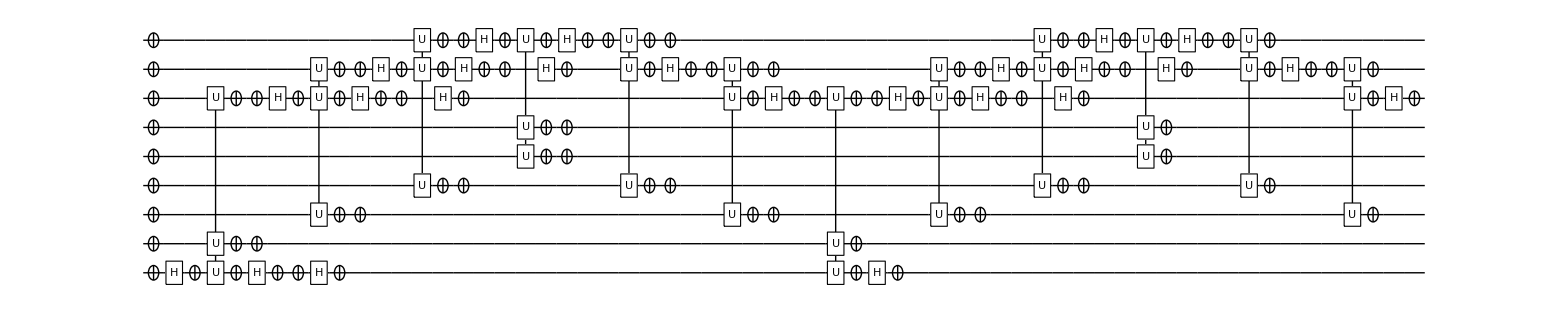

0

```mathematica
(*C4ZMat=DiagonalMatrix[Join[{1},Table[-1,{i,1,2^5-1}]]];
C4XMat=CalcCircuitMatrix[{Subscript[X, 1],Subscript[X, 2],Subscript[X, 3],Subscript[X, 4],Subscript[X, 0],Subscript[H, 0],Subscript[X, 0],Subscript[U, 0,1,2,3,4][C4ZMat],Subscript[X, 0],Subscript[H, 0],Subscript[X, 0],Subscript[X, 1],Subscript[X, 2],Subscript[X, 3],Subscript[X, 4]}];
C4XCirc={Subscript[X, 1],Subscript[X, 2],Subscript[X, 3],Subscript[X, 4],Subscript[X, 0],Subscript[H, 0],Subscript[X, 0],Subscript[U, 0,1,2,3,4][C4ZMat],Subscript[X, 0],Subscript[H, 0],Subscript[X, 0],Subscript[X, 1],Subscript[X, 2],Subscript[X, 3],Subscript[X, 4]};
C4ZCirc={Subscript[X, 1],Subscript[X, 2],Subscript[X, 3],Subscript[X, 4],Subscript[X, 0],Subscript[H, 0],Subscript[X, 0],Subscript[U, 0,1,2,3,4][C4XMat],Subscript[X, 0],Subscript[H, 0],Subscript[X, 0],Subscript[X, 1],Subscript[X, 2],Subscript[X, 3],Subscript[X, 4]};
C4XCircToff={Toff[0,6,1],Toff[6,7,2],Toff[7,8,3],Toff[8,4,5],Toff[7,8,3],Toff[6,7,2],Toff[0,6,1],Toff[6,7,2],Toff[7,8,3],Toff[8,4,5],Toff[7,8,3],Toff[6,7,2]};*)
C4XCircCCZ=Flatten[{ToffRyd[0,6,1],ToffRyd[6,7,2],ToffRyd[7,8,3],ToffRyd[8,4,5],ToffRyd[7,8,3],ToffRyd[6,7,2],ToffRyd[0,6,1],ToffRyd[6,7,2],ToffRyd[7,8,3],ToffRyd[8,4,5],ToffRyd[7,8,3],ToffRyd[6,7,2]}];
DrawCircuit[C4XCircCCZ]
Length[C5ZMat]
```

```mathematica
?Delete
```

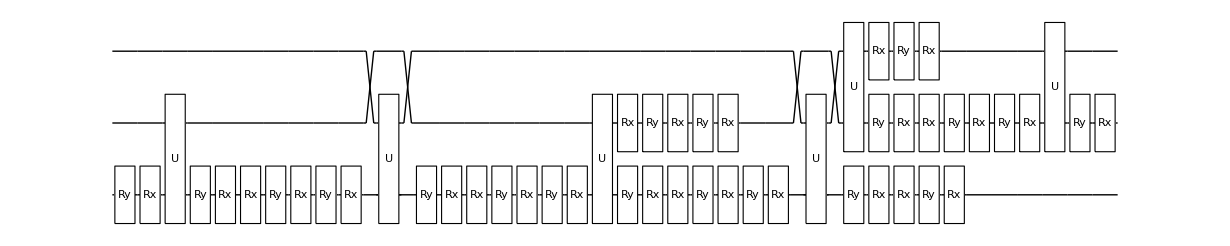

```mathematica
XTrans[i_]:={Subscript[Rx, i][Pi]};
HTrans[i_]:={Subscript[Ry, i][Pi/2],Subscript[Rx, i][Pi]};
HXTrans[q_]:=Subscript[Ry, q][Pi/2]
XHTrans[q_]:=Subscript[Ry, q][-Pi/2]
XHXTrans[q_]:={Subscript[Ry, q][-Pi/2],Subscript[Rx, q][-Pi]}
HXHTrans[q_]:={Subscript[Ry, q][-Pi],Subscript[Rx, q][-Pi]}
TGate[t_]:={Subscript[Rx, t][Pi/2],Subscript[Ry, t][-Pi/4],Subscript[Rx, t][-Pi/2]}
Tdg[t_]:={Subscript[Rx, t][Pi/2],Subscript[Ry, t][Pi/4],Subscript[Rx, t][-Pi/2]}
Subscript[CCZDecomp,t_,c1_,c2_]:=Flatten[{XHXTrans[t],Subscript[CZG, t,c1],XHXTrans[t], Tdg[t],XHXTrans[t],Subscript[CZG, t,c2],XHXTrans[t],TGate[t],XHXTrans[t],Subscript[CZG, t,c1],XHXTrans[t],Tdg[t],XHXTrans[t],Subscript[CZG, t,c2],XHXTrans[t],TGate[t],TGate[c1],XHXTrans[c1],Subscript[CZG, c1,c2],XHXTrans[c1],TGate[c2],Tdg[c1],XHXTrans[c1],Subscript[CZG, c1,c2],XHXTrans[c1]}]
DrawCircuit[ExtractCircuit[GetCircuitSchedule[Subscript[CCZDecomp, 0,1,2],RydDev,ReplaceAliases->True]]]
```

```mathematica
XHXTra
```

```mathematica
KetList[5][[1]][[2;;]]
```

{0,0,0,0}

```mathematica
CliffCCZRyd={HXTrans[0],HXTrans[0],Table[XTrans[i],{i,1,8}],Subscript[CCZ, 0,6,1],HXTrans[6],Subscript[CCZ, 7,6,2],HXTrans[7],Subscript[CCZ, 8,7,3],HXTrans[8],Subscript[CCZ, 8,5,4] XHTrans[8],Subscript[CCZ, 8,7,3]}
GroverIteration3Q[SearchSeed_]:=Module[{XIndices=Join[Position[Reverse[SearchSeed][[1]],1],Position[Reverse[SearchSeed][[2;;]],0]]},
Xs=Table[XTrans[XIndices[[j,1]]-1],{j,1,Length[XIndices]}];
Flatten[{Xs,Subscript[CCZ, 0,1,2],Xs,HTrans[0],HTrans[1],HTrans[2],Subscript[CCZ, 0,1,2],HTrans[0],HTrans[1],HTrans[2]}]]
```

```mathematica
?Replace
```

```mathematica
Print[KetList[6][[1]]]
C5XTranspiled=Flatten[{Table[XTrans[i],{i,1,8}],XTrans[0],HXTrans[0],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 8,7,3],HXTrans[8],Subscript[CCZ, 8,4,5],XHTrans[8],Subscript[CCZ, 8,7,3],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 3,7,8],HXTrans[8],Subscript[CCZ, 4,5,8],XHTrans[8],Subscript[CCZ, 3,8,7],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],,XHTrans[0],XTrans[0],Table[XTrans[i],{i,1,8}]}];
C5ZCliffTrans=Join[HTrans[0],C5XTranspiled,HTrans[0]];

GroverOracle6D3A[SearchSeed_]:=Module[{XIndices=Position[Reverse[SearchSeed][[2;;]],1]},
If[Reverse[SearchSeed][[1]]==0,XStart={XTrans[0],HXTrans[0],HXTrans[0]};XEnd={XHTrans[0],XHTrans[0],XTrans[0]},
XStart={HXTrans[0],HXTrans[0]};XEnd={XHTrans[0],XHTrans[0]}];
Xs=Flatten[Table[XTrans[XIndices[[j,1]]],{j,1,Length[XIndices]}]];
(*Print[Xs];*)
Flatten[{XStart,Xs,Table[XTrans[i],{i,6,8}],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 8,7,3],HXTrans[8],Subscript[CCZ, 8,4,5],XHTrans[8],Subscript[CCZ, 8,7,3],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 3,7,8],HXTrans[8],Subscript[CCZ, 4,5,8],XHTrans[8],Subscript[CCZ, 3,8,7],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Table[XTrans[i],{i,6,8}],Xs,XEnd}]]
GroverDiffusion6D3A=Flatten[{Table[HTrans[i],{i,0,5}],Table[XTrans[i],{i,6,8}],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 8,7,3],HXTrans[8],Subscript[CCZ, 8,4,5],XHTrans[8],Subscript[CCZ, 8,7,3],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 3,7,8],HXTrans[8],Subscript[CCZ, 4,5,8],XHTrans[8],Subscript[CCZ, 3,8,7],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Table[XTrans[i],{i,6,8}],Table[HTrans[i],{i,0,5}]}];
```

```mathematica
RenormList2Q=Table[{},{i,1,64}]

GroverOracle6D3A2Q[SearchSeed_]:=Module[{XIndices=Position[Reverse[SearchSeed][[2;;]],1]},
If[Reverse[SearchSeed][[1]]==0,XStart={XTrans[0],HXTrans[0],HXTrans[0]};XEnd={XHTrans[0],XHTrans[0],XTrans[0]},
XStart={HXTrans[0],HXTrans[0]};XEnd={XHTrans[0],XHTrans[0]}];
Xs=Flatten[Table[XTrans[XIndices[[j,1]]],{j,1,Length[XIndices]}]];
(*Print[Xs];*)
Flatten[{XStart,Xs,Table[XTrans[i],{i,6,8}],Subscript[CCZDecomp, 0,1,6],HXTrans[6],Subscript[CCZDecomp, 2,6,7],HXTrans[7],Subscript[CCZDecomp, 8,7,3],HXTrans[8],Subscript[CCZDecomp, 8,4,5],XHTrans[8],Subscript[CCZDecomp, 8,7,3],XHTrans[7],Subscript[CCZDecomp, 2,6,7],XHTrans[6],Subscript[CCZDecomp, 0,1,6],HXTrans[6],Subscript[CCZDecomp, 2,6,7],HXTrans[7],Subscript[CCZDecomp, 3,7,8],HXTrans[8],Subscript[CCZDecomp, 4,5,8],XHTrans[8],Subscript[CCZDecomp, 3,8,7],XHTrans[7],Subscript[CCZDecomp, 2,6,7],XHTrans[6],Table[XTrans[i],{i,6,8}],Xs,XEnd}]]

GroverDiffusion6D3A2Q=Flatten[{Table[HTrans[i],{i,0,5}],Table[XTrans[i],{i,6,8}],Subscript[CCZDecomp, 0,1,6],HXTrans[6],Subscript[CCZDecomp, 2,6,7],HXTrans[7],Subscript[CCZDecomp, 8,7,3],HXTrans[8],Subscript[CCZ, 8,4,5],XHTrans[8],Subscript[CCZDecomp, 8,7,3],XHTrans[7],Subscript[CCZDecomp, 2,6,7],XHTrans[6],Subscript[CCZDecomp, 0,1,6],HXTrans[6],Subscript[CCZDecomp, 2,6,7],HXTrans[7],Subscript[CCZDecomp, 3,7,8],HXTrans[8],Subscript[CCZDecomp, 4,5,8],XHTrans[8],Subscript[CCZDecomp, 3,8,7],XHTrans[7],Subscript[CCZDecomp, 2,6,7],XHTrans[6],Table[XTrans[i],{i,6,8}],Table[HTrans[i],{i,0,5}]}];

GroverAlg6D3A2Q[SearchSeed_]:=Flatten[Join[Table[HTrans[i],{i,0,5}],Table[{GroverOracle6D3A2Q[SearchSeed],GroverDiffusion6D3A2Q},{j,1,8}]]]

GroverDataUnNormCZ=Table[If[IntegerQ[i/8],Print[i]];SearchSeed=KetList[6][[i]];
ρ=CreateDensityQureg[9];
InitZeroState[ρ];
ApplyCircuit[ρ,ExtractCircuit[InsertCircuitNoise[GroverAlg6D3A2Q[SearchSeed],RydDev,ReplaceAliases->True]]];
Renorm=Total[CalcProbOfAllOutcomes[ρ,Range[0,8]]];
RenormList2Q[[i]]=Renorm;
CalcProbOfAllOutcomes[ρ,{0,1,2,3,4,5}],{i,1,64}];

RenormData2Q=Table[{i,RenormList2Q[[i]]},{i,1,64}]
GroverDataUnnorm2Q=Table[{i,GroverDataUnNormCZ[[i,i]]±StandardDeviation[Diagonal[GroverDataUnNormCZ]]},{i,1,64}]
GroverDataRenorm2Q=Table[{i,GroverDataUnNormCZ[[i,i]]/RenormList2Q[[i]]±StandardDeviation[Diagonal[GroverDataUnNormCZ/RenormList2Q]]},{i,1,64}]
```

{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

8

```mathematica
RenormList=Table[{},{i,1,64}]

GroversAlg6D3A[SearchSeed_]:=Flatten[Join[Table[HTrans[i],{i,0,5}],Table[{GroverOracle6D3A[SearchSeed],GroverDiffusion6D3A},{j,1,8}]]]
GroverDataUnNormCCZ=Table[If[IntegerQ[i/8],Print[i]];SearchSeed=KetList[6][[i]];
ρ=CreateDensityQureg[9];
InitZeroState[ρ];
ApplyCircuit[ρ,ExtractCircuit[InsertCircuitNoise[GroversAlg6D3A[SearchSeed],RydDev,ReplaceAliases->True]]];
Renorm=Total[CalcProbOfAllOutcomes[ρ,Range[0,8]]];
RenormList[[i]]=Renorm;
CalcProbOfAllOutcomes[ρ,{0,1,2,3,4,5}],{i,1,64}];

RenormData=Table[{i,RenormList[[i]]},{i,1,64}]
GroverDataUnnorm=Table[{i,GroverDataUnNormCCZ[[i,i]]±StandardDeviation[Diagonal[GroverDataUnNormCCZ]]},{i,1,64}]
GroverDataRenorm=Table[{i,GroverDataUnNormCCZ[[i,i]]/RenormList[[i]]±StandardDeviation[Diagonal[GroverDataUnNormCCZ/RenormList]]},{i,1,64}]

(*DrawCircuit[GroverOracle6D3A[KetList[6][[1]]]]
DrawCircuit[ExtractCircuit[GetCircuitSchedule[C5XTranspiled,RydDev,ReplaceAliases->True]]]*)
(*ExtractCircuit[GetCircuitSchedule[C5XTranspiled,RydDev,ReplaceAliases->True]]*)
```

{0,0,0,0,0,0}

{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

8

16

24

32

40

48

56

64

{{1,0.458395},{2,0.458396},{3,0.458395},{4,0.458395},{5,0.458395},{6,0.458396},{7,0.458395},{8,0.458395},{9,0.458395},{10,0.458396},{11,0.458395},{12,0.458395},{13,0.458395},{14,0.458396},{15,0.458396},{16,0.458395},{17,0.458395},{18,0.458395},{19,0.458395},{20,0.458395},{21,0.458395},{22,0.458396},{23,0.458395},{24,0.458395},{25,0.458395},{26,0.458396},{27,0.458395},{28,0.458395},{29,0.458396},{30,0.458396},{31,0.458396},{32,0.458395},{33,0.458395},{34,0.458395},{35,0.458395},{36,0.458395},{37,0.458395},{38,0.458396},{39,0.458395},{40,0.458395},{41,0.458395},{42,0.458396},{43,0.458395},{44,0.458395},{45,0.458396},{46,0.458396},{47,0.458396},{48,0.458395},{49,0.458396},{50,0.458396},{51,0.458396},{52,0.458396},{53,0.458396},{54,0.458396},{55,0.458396},{56,0.458396},{57,0.458396},{58,0.458396},{59,0.458396},{60,0.458396},{61,0.458396},{62,0.458396},{63,0.458396},{64,0.458396}}

{{1,0.327821±5.0796×10^-6},{2,0.327831±5.0796×10^-6},{3,0.327824±5.0796×10^-6},{4,0.327822±5.0796×10^-6},{5,0.327824±5.0796×10^-6},{6,0.327833±5.0796×10^-6},{7,0.327826±5.0796×10^-6},{8,0.327825±5.0796×10^-6},{9,0.327824±5.0796×10^-6},{10,0.327833±5.0796×10^-6},{11,0.327826±5.0796×10^-6},{12,0.327825±5.0796×10^-6},{13,0.327826±5.0796×10^-6},{14,0.327835±5.0796×10^-6},{15,0.327829±5.0796×10^-6},{16,0.327827±5.0796×10^-6},{17,0.327819±5.0796×10^-6},{18,0.327827±5.0796×10^-6},{19,0.327821±5.0796×10^-6},{20,0.32782±5.0796×10^-6},{21,0.327821±5.0796×10^-6},{22,0.32783±5.0796×10^-6},{23,0.327824±5.0796×10^-6},{24,0.327822±5.0796×10^-6},{25,0.327821±5.0796×10^-6},{26,0.32783±5.0796×10^-6},{27,0.327824±5.0796×10^-6},{28,0.327822±5.0796×10^-6},{29,0.327824±5.0796×10^-6},{30,0.327833±5.0796×10^-6},{31,0.327827±5.0796×10^-6},{32,0.327825±5.0796×10^-6},{33,0.327819±5.0796×10^-6},{34,0.327827±5.0796×10^-6},{35,0.327821±5.0796×10^-6},{36,0.32782±5.0796×10^-6},{37,0.327821±5.0796×10^-6},{38,0.32783±5.0796×10^-6},{39,0.327824±5.0796×10^-6},{40,0.327822±5.0796×10^-6},{41,0.327821±5.0796×10^-6},{42,0.32783±5.0796×10^-6},{43,0.327824±5.0796×10^-6},{44,0.327822±5.0796×10^-6},{45,0.327824±5.0796×10^-6},{46,0.327833±5.0796×10^-6},{47,0.327827±5.0796×10^-6},{48,0.327825±5.0796×10^-6},{49,0.327826±5.0796×10^-6},{50,0.327835±5.0796×10^-6},{51,0.327829±5.0796×10^-6},{52,0.327827±5.0796×10^-6},{53,0.327829±5.0796×10^-6},{54,0.327838±5.0796×10^-6},{55,0.327832±5.0796×10^-6},{56,0.32783±5.0796×10^-6},{57,0.327829±5.0796×10^-6},{58,0.327838±5.0796×10^-6},{59,0.327832±5.0796×10^-6},{60,0.32783±5.0796×10^-6},{61,0.327832±5.0796×10^-6},{62,0.327841±5.0796×10^-6},{63,0.327835±5.0796×10^-6},{64,0.327833±5.0796×10^-6}}

{{1,0.71515±0.0000106938},{2,0.71517±0.0000106938},{3,0.715155±0.0000106938},{4,0.715152±0.0000106938},{5,0.715155±0.0000106938},{6,0.715174±0.0000106938},{7,0.715161±0.0000106938},{8,0.715158±0.0000106938},{9,0.715155±0.0000106938},{10,0.715174±0.0000106938},{11,0.715161±0.0000106938},{12,0.715157±0.0000106938},{13,0.715161±0.0000106938},{14,0.715179±0.0000106938},{15,0.715167±0.0000106938},{16,0.715163±0.0000106938},{17,0.715144±0.0000106938},{18,0.715163±0.0000106938},{19,0.71515±0.0000106938},{20,0.715146±0.0000106938},{21,0.71515±0.0000106938},{22,0.715168±0.0000106938},{23,0.715156±0.0000106938},{24,0.715152±0.0000106938},{25,0.71515±0.0000106938},{26,0.715168±0.0000106938},{27,0.715156±0.0000106938},{28,0.715152±0.0000106938},{29,0.715155±0.0000106938},{30,0.715174±0.0000106938},{31,0.715161±0.0000106938},{32,0.715158±0.0000106938},{33,0.715144±0.0000106938},{34,0.715163±0.0000106938},{35,0.71515±0.0000106938},{36,0.715146±0.0000106938},{37,0.71515±0.0000106938},{38,0.715168±0.0000106938},{39,0.715156±0.0000106938},{40,0.715152±0.0000106938},{41,0.71515±0.0000106938},{42,0.715168±0.0000106938},{43,0.715156±0.0000106938},{44,0.715152±0.0000106938},{45,0.715155±0.0000106938},{46,0.715174±0.0000106938},{47,0.715161±0.0000106938},{48,0.715158±0.0000106938},{49,0.715161±0.0000106938},{50,0.715179±0.0000106938},{51,0.715166±0.0000106938},{52,0.715163±0.0000106938},{53,0.715166±0.0000106938},{54,0.715185±0.0000106938},{55,0.715172±0.0000106938},{56,0.715169±0.0000106938},{57,0.715166±0.0000106938},{58,0.715185±0.0000106938},{59,0.715172±0.0000106938},{60,0.715169±0.0000106938},{61,0.715172±0.0000106938},{62,0.71519±0.0000106938},{63,0.715178±0.0000106938},{64,0.715174±0.0000106938}}

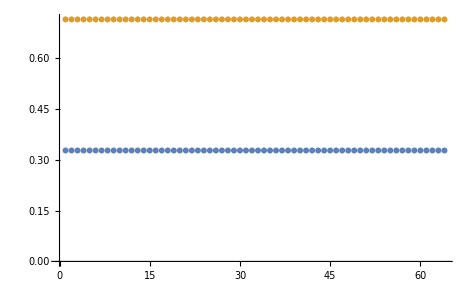

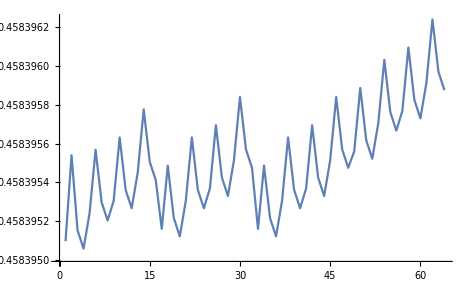

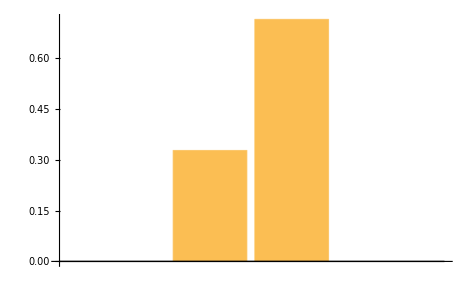

```mathematica
ListPlot[{GroverDataUnnorm,GroverDataRenorm}]
ListLinePlot[RenormData]
BarChart[{(Mean[Diagonal[GroverDataUnNormCCZ]])±StandardDeviation[Diagonal[GroverDataUnNormCCZ]]/8,(Mean[Diagonal[GroverDataUnNormCCZ]]/Mean[RenormList])±StandardDeviation[Diagonal[GroverDataUnNormCCZ]]/8}]
```

```mathematica
RenormList
```

{0.458395,0.458396,0.458395,0.458395,0.458395,0.458396,0.458395,0.458395,0.458395,0.458396,0.458395,0.458395,0.458395,0.458396,0.458396,0.458395,0.458395,0.458395,0.458395,0.458395,0.458395,0.458396,0.458395,0.458395,0.458395,0.458396,0.458395,0.458395,0.458396,0.458396,0.458396,0.458395,0.458395,0.458395,0.458395,0.458395,0.458395,0.458396,0.458395,0.458395,0.458395,0.458396,0.458395,0.458395,0.458396,0.458396,0.458396,0.458395,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396}

```mathematica
ρ=CreateQureg[9]

Table[InitZeroState[ρ];InputState=KetList[6][[i]];
XIndices=Position[Reverse[InputState],1];
Xs=Table[Subscript[X,XIndices[[j,1]]-1],{j,1,Length[XIndices]}];
ApplyCircuit[ρ,Xs];
ApplyCircuit[ρ,ExtractCircuit[GetCircuitSchedule[Subscript[CCZDecomp, 0,1,2](*GroverOracle6D3A[InputState[1]]*)(*C5XTranspiled*)(*C5ZTrans*),RydDev,ReplaceAliases->True]]];
(*GetAmp[ρ,i-1,i-1]*)Chop[GetQuregMatrix[ρ][[1;;2^3]]],{i,1,8}]//MatrixForm
(*C5XCircCCZ=Flatten[{Table[HTrans[i],{i,0,5}],ToffRyd[0,6,1],ToffRyd[6,7,2],ToffRyd[7,8,3],ToffRyd[8,4,5],ToffRyd[7,8,3],ToffRyd[6,7,2],ToffRyd[0,6,1],ToffRyd[6,7,2],ToffRyd[7,8,3],ToffRyd[8,4,5],ToffRyd[7,8,3],ToffRyd[6,7,2],Table[HTrans[i],{i,0,5}]}];*)
DestroyAllQuregs[];
```

0

(-0.92388-0.382683 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.92388+0.382683 ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.92388+0.382683 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.92388+0.382683 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.92388+0.382683 ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.92388+0.382683 ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.92388+0.382683 ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.92388+0.382683 ⅈ)

```mathematica
?QuEST`*
```

```mathematica
?Round
```

```mathematica
Sqrt[64]
```

```mathematica
CCZDecomp[t_,c1_,c2_]:=
```

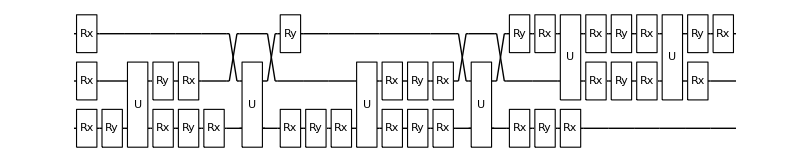

{Rx_1[-1.981],Rx_2[-2.6423],Ry_1[π/2],Ry_2[π/2],CZG_(0,1),Rx_0[π/2],Ry_0[π/4],Rx_0[-π/2],Rx_1[π/2],Ry_1[3.0061],Rx_1[π/2],CZG_(0,2),Rx_0[-π/2],Ry_0[π/4],Rx_0[-π/2],Rx_2[-π/2],Rx_2[2.702],Rx_2[π/2],CZG_(0,1),Rx_0[π/2],Ry_0[(3 π)/4],Rx_1[-2.7048],Ry_1[0.89527],Rx_0[π/2],Rx_1[0.92944],CZG_(0,2),Rx_0[-π/2],Ry_0[π/4],Rx_0[π/2],Rx_2[-π/2],Ry_2[0.93891],CZG_(1,2),Rx_1[π/2],Ry_1[π/2],Rx_1[π/2],Rx_2[π/4],Ry_2[π/2],Rx_2[-π/2],CZG_(1,2),Rx_1[-π/2],Ry_1[π/4],Rx_1[-π/2],Rx_2[π/2]}

{Rx_1[-1.981],Rx_2[-2.6423],Ry_1[π/2],Ry_2[π/2],CZG_(0,1),Rx_0[π/2],Ry_0[π/4],Rx_0[-π/2],Rx_1[π/2],Ry_1[3.0061],Rx_1[π/2],CZG_(0,2),Rx_0[-π/2],Ry_0[π/4],Rx_0[-π/2],Rx_2[-π/2],Ry_2[2.702],Rx_2[π/2],CZG_(0,1),Rx_0[π/2],Ry_0[(3 π)/4],Rx_1[-2.7048],Ry_1[0.89527],Rx_0[π/2],Rx_1[0.92944],CZG_(0,2),Rx_0[-π/2],Ry_0[π/4],Rx_0[π/2],Rx_2[-π/2],Ry_2[0.93891],CZG_(1,2),Rx_1[π/2],Ry_1[π/2],Rx_1[π/2],Rx_2[π/4],Ry_2[π/2],Rx_2[-π/2],CZG_(1,2),Rx_1[-π/2],Ry_1[π/4],Rx_1[-π/2],Rx_2[π/2]}

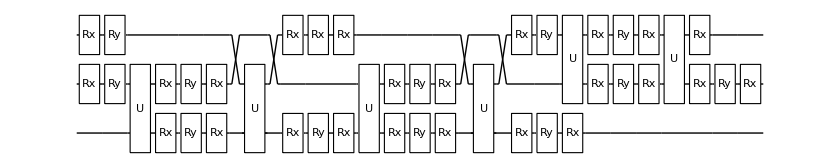

InsertCircuitNoise::error: Encountered gate CZ_(0,1) which is not supported by the given device specification. Note this may be due to preceding gates, if the spec contains constraints which depend on dynamic variables. See ?GetUnsupportedGates.

ExtractCircuit::error: Invalid arguments. See ?ExtractCircuit

CalcCircuitMatrix::error: Invalid arguments. See ?CalcCircuitMatrix

```mathematica
TGate[t_]:={Subscript[Rx, t][Pi/2],Subscript[Ry, t][-Pi/4],Subscript[Rx, t][-Pi/2]}
Tdg[t_]:={Subscript[Rx, t][Pi/2],Subscript[Ry, t][Pi/4],Subscript[Rx, t][-Pi/2]}






{Subscript[Rx, t][-0.09065988720074536],Subscript[Ry, t][-Pi/2],Subscript[Rx, c1][-Pi],Subscript[Rx, c2][-Pi],Subscript[CZG, t,c1],Subscript[Rx, t][-0.800360109933159],Subscript[Ry, t][1.372292382481866],Subscript[Rx, t][1.63614359593572],Subscript[Ry, c1][-Pi],Subscript[Rx, c1][-Pi],Subscript[CZG, t,c2],Subscript[Rx, t][2.3583],Subscript[Ry, t][0.82493],Subscript[Rx, t][-2.7641],Subscript[Ry, c2][Pi],Subscript[CZG, t,c1],Subscript[Rx, t][-0.12796],Subscript[Ry, t][0.68257],Subscript[Rx, t][-2.5412],Subscript[Rx, c1][-π/2],Subscript[Ry, c1][Pi/4],Subscript[Rx, c1][-π/2],Subscript[CZG, t,c2],Subscript[Rx, t][-2.7055],Subscript[Ry, t][2.2467],Subscript[Rx, t][2.211],Subscript[Ry, c2][-π/2],Subscript[Rx, c2][Pi/2],Subscript[CZG, c1,c2],Subscript[Rx, c1][π/2],Subscript[Ry, c1][Pi/2],Subscript[Rx, c1][Pi/2],Subscript[Rx, c2][Pi/4],Subscript[Ry, c2][Pi/2],Subscript[Rx, c2][-Pi/2],Subscript[CZG, c1,c2],Subscript[Rx, c1][-Pi],Subscript[Ry, c2][-Pi/4],Subscript[Rx, c2][-Pi/2]};

DrawCircuit[ExtractCircuit[GetCircuitSchedule[CCZDecomp[0,1,2],RydDev,ReplaceAliases->True]]]//MatrixForm
```

```mathematica
?QuEST`*
```